# Conway's Game of Life

## Program by Abigail Fisher, Marissa Neal (former Smithies), Kapil Easwar (son of emerita Prof. Nalini Easwar) and Christophe Golé.

## About Conway's Game of Life

### Rules of the Game

This is taken from Wikipedia:
"The universe of the Game of Life is an infinite two-dimensional orthogonal grid of square cells, each of which is in one of two possible states, live or dead. Every cell interacts with its eight neighbours, which are the cells that are horizontally, vertically, or diagonally adjacent. At each step in time, the following transitions occur:

   1. Any live cell with fewer than two live neighbours dies, as if caused by under-population.
   2. Any live cell with two or three live neighbours lives on to the next generation.
   3. Any live cell with more than three live neighbours dies, as if by overcrowding.
   4. Any dead cell with exactly three live neighbours becomes a live cell, as if by reproduction.

The initial pattern constitutes the seed of the system. The first generation is created by applying the above rules simultaneously to every cell in the seed—births and deaths occur simultaneously, and the discrete moment at which this happens is sometimes called a tick (in other words, each generation is a pure function of the preceding one). The rules continue to be applied repeatedly to create further generations."

In our first rendition, we will make the grid finite, and assume that all the cells outside of the finite universe are dead and can't be revived. In a second rendition, you will be asked to extend the universe periodically in both directions, as if on a torus!

The game of life is an example of cellular automaton, where cells on a grid are updated according to  rules involving the state of surrounding cells. Cellular automata can be viewed as dynamical systems where both the time and space are discrete (if a cell can only have finitely many states).

## Simulating the game of life

A universe in this game is a matrix of 0' s (dead cells - in white here) and 1' s (live cells, in green here) .  
The function univplot plots this matrix as a grid, coloring the live cells (Green is default) . 
The function getUniverse allows you to input such a matrix and modify it at will by clicking on the cells . You can also create a universe with cells randomly assigned to be alive or dead. 
The game of life can then be applied repeatedly with an initial universe of your choice, using the function ourlife.

#### Creating a blank universe and plotting it with univplot

```mathematica
dimuniv = 20;
univ= Table[0, dimuniv, dimuniv];
univplot[univ]
```

#### Customizing a universe with getUniverse

Usually start with a blank universe and create the pattern you want by clicking on cells to switch their status. You can also put any of the universes proposed in the sections below, and change them.

```mathematica
getUniverse[univ]
```

#### Alternatively, create a random universe

```mathematica
univ = Table[Random[Integer, {0,1}], {20}, {20}];
```

#### Simulating the game of life with ourlife

Execute the following code repeatedly

```mathematica
univplot[univ]
univ = ourlife[univ];
Count[Flatten[univ], 1]
```

#### Iterating a prescribed number of iterates, using Nest

```mathematica
nourlife[univ_, n_] := Nest[ourlife, univ, n]
```

```mathematica
newuniv =nourlife[glideruniv, 50];
univplot[newuniv]
```

## Tasks: Getting to know the game

To explore the game, answer these questions. You will want to use the section above to create initial universes, and modify them by hand (clicking on cells to turn them alive or dead)

#### 1) What happens to a universe with only one live cell in it? Come up with other universes that behave in the same way. What about 2 adjacent cells? 3 cells in a row? universe with only one cell will always immediately die because it does not survive past one iteration due to rule one. universe with 2 cells is the same as one cell alive, though if it is on the edge the board becomes a donut and so it would transfer live cells etc. keep them alive longer. universe with three cells in a row is periodic. and will look like a plus sign shape alternating poles.

#### 2) What happens to the following universe? Come up with other universes that behave in the same way. this universe is fixed as the center two pieces are dead by overcrowding at all times. it will stay

#### 3) Find a universe of period 2. That is, a universe that is the same every other step. this would be three live cells in a row or column.

#### 4) Can you go backward with the game of life, i.e. can you guess the past from the present? you can know Any variation of the past, but not the SPECIFIC past of that specific pattern.

#### 5) The following pattern is called a "glider" try to guess why, by representing a few iterates “by hand” (4 or 5 five is a good number...). You can verify your answer by iterating the "ourlife" function. this patterns moves diagonally across the screen.

#### 6) Create a universe that’s half alive on one side, half dead on the other, and guess it evolution under the game of life. Check your answer with ourlife. -Graphics- left side stops after a few iterations, but the right side keeps going infinitely in period

#### Creating a Glider universe

```mathematica
dimuniv = 20;
glideruniv = Table[0, dimuniv, dimuniv];
glideruniv[[2, 3]]=1; glideruniv[[3, 4]]=1;  glideruniv[[4, 2]]=1;glideruniv[[4, 3]]=1; glideruniv[[4, 4]]=1; 
univplot[glideruniv]
univ = glideruniv;
```

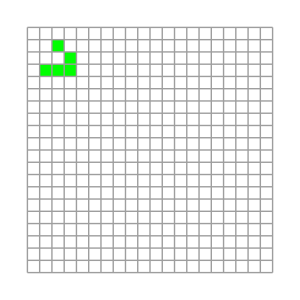

## Inside the hood

## Code for initiating a universe and graphing it (getUniverse, univplot)

### Default Parameters

```mathematica
(* Maximum size of the universe's picture, in pixels *)
IMAGESIZE = 300;

(* assigns a value of 1 to a live cell, 0 to a dead cell *)
LIFE=1;
DEATH=0;

(* colors representing "alive" and "dead" cells *)
LIFECOLOR=Green;   (* alive *)
DEATHCOLOR=White;  (*dead *)
```

### Universe graphing function univplot

```mathematica
univplot[univ_]:=ArrayPlot[univ, Mesh->True, ColorRules->{1->Green,0->White},Axes->False,ImageSize->IMAGESIZE
]
```

### Interactive universe initialization function getUNiverse - Edit at your own risks!

```mathematica
(* takes a pixel coordinate and converts it to a box index *)
boxIndex[{inx_,iny_}, NUMX_, NUMY_]:=Block[{x,y,j,i},
{x,y}={inx,1-iny};
j=1+Floor[x*NUMX];
i=1+Floor[y*NUMY];
Return[{i,j}];
];

getUniverse[inituniv_]:=Module[{numx, numy},

(* get the dimensions, initialize the universe *)
{numy, numx} = Dimensions[inituniv];
univ = inituniv;

(* Create the editable universe pane *)
ClickPane[
Dynamic@univplot[univ],
(
{i,j}=boxIndex[#/{numx,numy}, numx, numy];
univ[[i,j]]=univ[[i,j]]/.{LIFE->DEATH, DEATH-> LIFE}
)&
]


]
```

## The Game of Life Code (ourlife)

```mathematica
(* Sum the 8 neighbors at each point, arranged as they would be  *)
sumnear[j_,k_,univ_]:=
univ[[j-1, k-1]]+univ[[j-1, k]]+univ[[j-1, k+1]]+ univ[[j, k-1]]                                           +univ[[j, k+1]]+
univ[[j+1, k-1]]+univ[[j+1, k]]+univ[[j+1, k+1]];

(* this is the updating function for the Game of Life *)
ourlife[univ_]:= Module[{newuniv},
biguniv = ArrayPad[univ, 1]; (* puts a layer of 0's around the universe *)
newuniv =Table[
Which[
biguniv[[i, j]]==1&&  sumnear[i, j, biguniv] < 2, 0, 
biguniv[[i, j]]==1 && ( sumnear[i, j, biguniv]==2||sumnear[i, j, biguniv] ==3),1, 
biguniv[[i, j]]==1 &&  sumnear[i, j, biguniv] > 3,0 , 
biguniv[[i, j]]==0 &&  sumnear[i, j, biguniv] ==3,1,
biguniv[[i, j]]==0 && sumnear[i, j, biguniv] ≠ 3, 0], 
{i,2, Dimensions[biguniv][[1]]-1}, {j,2, Dimensions[biguniv][[2]]-1}];
 Return[newuniv]  (* Return gets this variable out of the Module *)
];
```

## Showing evolution of a universe as an animation

Initialize your universe (you can choose other initial universes, of course)

```mathematica
univ = Table[Random[Integer, {0,1}], {20}, {20}];
```

Customize your universe

```mathematica
getUniverse[univ]
```

Compute and store a bunch of iterates, then manipulate them.

```mathematica
numgen =50;univevolution = Table[univ=ourlife[univ], {numgen}];
```

```mathematica
Manipulate[univplot[univevolution[[k]]], {k,1, numgen,1}]
```

Or compute and show them on the go ( alittle more sluggish than the previous solution?):

```mathematica
Manipulate[univplot[nourlife[univ, k]], {k,1, numgen,1}]
```

## Tasks 2: Modify the Life game to "run on a torus" (lifetorus)

Modify the "life" code so that cells on the left edges are neighbors of corresponding cells on the right edge, and likewise for the top and bottom edges.
It turns out that the only difference is in the use of the option “Periodic” in the ArrayPad function used in “ourlife”:

```mathematica
m = {{2,2,4,5},{4,3,5,1},{1,4,0,4}};
%//MatrixForm
ArrayPad[m,1];
%//MatrixForm
ArrayPad[m,1, "Periodic"];
%//MatrixForm
```

### “lifetorus” program: ourlife on a torus

```mathematica
(* Sum the 8 neighbors at each point, arraged as they would be  *)
sumnear[j_,k_,univ_]:=
univ[[j-1, k-1]]+univ[[j-1, k]]+univ[[j-1, k+1]]+ univ[[j, k-1]]                                           +univ[[j, k+1]]+
univ[[j+1, k-1]]+univ[[j+1, k]]+univ[[j+1, k+1]];

lifetorus[univ_]:= Module[{newuniv, biguniv },
biguniv = ArrayPad[univ, 1,  "Periodic"]; (* the only difference with the previous code!!! *) 

newuniv = Table[
If[
(univ[[i,j]]==1 &&(sumnear[i+1,j+1, biguniv]==2 ||sumnear[i+1,j+1, biguniv]==3)) || (biguniv[[i+1,j+1]]==0 && sumnear[i+1,j+1, biguniv] ==3),
1,0
] 
,{i,1, Dimensions[univ][[1]]}, {j,1, Dimensions[univ][[2]]}];
 Return[newuniv]  (* Return gets this variable out of the Module *)
];
```

### Using the “lifetorus” program

#### initialize your universe (with a random universe here)

```mathematica
univ = Table[Random[Integer, {0,1}], {30}, {30}];
getUniverse[univ]
```

#### Iterate lifetorus

```mathematica
univplot[univ]
univ = lifetorus[univ];
```

#### Animate lifetorus: Glider example

Initialize your glider universe:

```mathematica
dimuniv = 20;
glideruniv = Table[0, dimuniv, dimuniv];
glideruniv[[2, 3]]=1; glideruniv[[3, 4]]=1;  glideruniv[[4, 2]]=1;glideruniv[[4, 3]]=1;glideruniv[[4, 4]]=1;
```

Iterate the torus game of life “numgen” times, recording each generations (careful, your computer can bug down in the animation for numgen too high):

```mathematica
univ=glideruniv;
numgen =100;univevolution = Table[univ=lifetorus[univ], {numgen}];
univevolution = Prepend[univevolution,glideruniv];
```

Manipulate to visualize the evolution of your universe under the torus game of life

```mathematica
Manipulate[univplot[univevolution[[k]]], {k,1, numgen,1}]
```